```mathematica
SetDirectory["~/mathematica/tomography"]
```

index of refraction, SU8
  8 keV     delta=3.801*10^-6   beta=5.137*10^-8     lambda = 1.54*10^-10
10 keV    delta=2.461*10^-6   beta=2.273*10^-8    lambda = 1.24*10^-10
12 keV  delta=1.694*10^-6   beta=1.126*10^-8   lambda = 1.03*10^-10

```mathematica
<<PhysicalConstants`;
c=SpeedOfLight Second/Meter;
h=PlanckConstant Convert[1 Joule,ElectronVolt]/Joule/Second/ElectronVolt;
lambda=1.03*10^-10;
k=(2π)/lambda;
delta=1.694*10^-6 ;
beta=1.126*10^-8;
size=32; (*size of the matrix*)
r=1*10^-6; (*period*)
limitn=0.7*10^-6; (* limit of calculation: range = (-limit, limit)*)
limitm=0.7*10^-6;
Np=Floor[2*limitn/r]; (* number of periods*)
stepn=2*limitn/(size-1);
stepm=2*limitm/(size-1);
optthick=lambda/(2*delta)*10^6;
t=lambda/(2*delta);(*grating thickness*)
phi=(2π)/lambda*delta*t; (*phase shift*)
mu=(4π)/lambda*beta; (* absorption coefficient m^-1*)
z=0.05*10^-4; (*distance from the object*)

TableForm[{{"lambda","",lambda},{"delta","",delta},{"beta","",beta},{"size","size of the matrix",size},{"r","period",r},{"limitn","limit of calculation",limitn},{"limitm","limit of calculation",limitm},{"Np","number of periods",Np},{"stepn","",stepn},{"stepm","",stepm},{"optthick","",optthick},{"t","grating thickness",t},{"phi","phase shift",phi},{"mu","absorption coefficient m^-1",mu},{"z","distance from the object",z}}]
```

lambda |  | 1.03×10^-10
delta |  | 1.694×10^-6
beta |  | 1.126×10^-8
size | size of the matrix | 32
r | period | 1/1000000
limitn | limit of calculation | 7.×10^-7
limitm | limit of calculation | 7.×10^-7
Np | number of periods | 1
stepn |  | 4.51613×10^-8
stepm |  | 4.51613×10^-8
optthick |  | 30.4014
t | grating thickness | 0.0000304014
phi | phase shift | 3.14159
mu | absorption coefficient m^-1 | 1373.76
z | distance from the object | 5.×10^-6

```mathematica
(*ff=Random[Real,{-limitn,limitn}];gg=Random[Real,{-limitm,limitm}];*)object=Table[If[(m-1.5r)^2+(n)^2≤(r)^2, Exp[I*phi], 0]+If[(m-1.5r)^2+(n)^2>(r)^2,If[(m+1.5r)^2+(n)^2≤(r)^2,  Exp[-mu*t], 1],0],{n,-limitn,limitn,stepn},{m,-limitm,limitm,stepm}];
ListDensityPlot[Arg@object]
```

```mathematica
{10^3*N[(limitm^4/(2*lambda))^(1/3)],limitm^2/(4*lambda)}
```

{0.0105239,0.00118932}

```mathematica
(*Export["radiography.dat",Abs[object]^2]*)
```

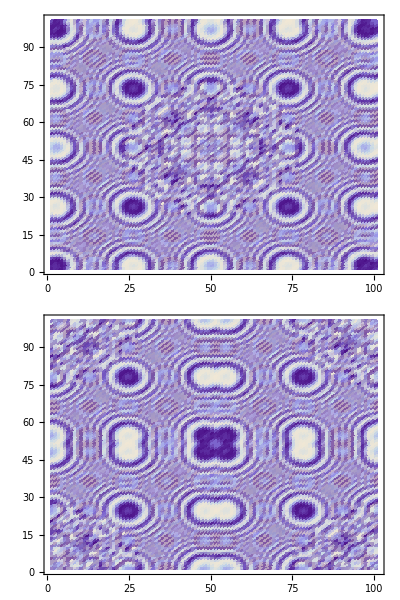

```mathematica
Block[{spar,ar,far,prop,fprop,directInt,pp,gg,hh,campo,campo2,plist,pmlist,fpfa,
size=100,height=1,z=0.05 10^-4,lambda=1.03*10^-10,k},
k=(2π)/lambda;

spar[siz_,hei_:100]:=SparseArray[{{siz/2+1,siz/2+1}->hei},{siz+1,siz+1}];
(*spar[size_,height_:100]:=SparseArray[
Join[
Table[{size/2+1,i}->height,{i,1,size+1}],Table[{i,size/2+1}->height,{i,1,size+1}]
],{size+1,size+1}
];*)

ar=spar[size,height];
far=Fourier[ar];
pmlist=Table[(-1)^(i+j),{i,-size/2,size/2},{j,-size/2,size/2}];

prop=Table[1/(I*lambda*z)Exp[-I*k*z]*Exp[-I*k*(n^2+m^2)/(2*z)],{n,-size/2,size/2},{m,-size/2,size/2}];
fprop=Fourier[prop];
fpfa=fprop*far;
directInt=InverseFourier[fpfa];
pp=RotateRight[directInt,Floor[Length[directInt]/2]];
gg=Transpose[pp];
hh=RotateRight[gg,Floor[Length[directInt]/2]];
campo=Transpose[hh];
campo2=campo*Abs[1-ar];
(*TableForm@{ListDensityPlot[Re@far,PerformanceGoal->"Quality"],
ListDensityPlot[Re@directInt,PerformanceGoal->"Quality"],
ListDensityPlot[Re@pp,PerformanceGoal->"Quality"],
ListDensityPlot[Re@gg,PerformanceGoal->"Quality"],
ListDensityPlot[Re@hh,PerformanceGoal->"Quality"],
ListDensityPlot[Re@campo,PerformanceGoal->"Quality"]}*)

(*TableForm@{
{Timing@ListDensityPlot[ar,PerformanceGoal->"Quality"]},
{ListDensityPlot[Re@far,PerformanceGoal->"Quality"],
ListDensityPlot@Im@far,
ListDensityPlot@Arg@far,
ListDensityPlot@Abs@far},
{ListDensityPlot@Re@campo,
ListDensityPlot@Im@campo,
ListDensityPlot@Arg@campo,
ListDensityPlot@Abs@campo},
{ListDensityPlot@Re@campo2,
ListDensityPlot@Im@campo2,
ListDensityPlot@Arg@campo2,
ListDensityPlot@Abs@campo2}
}*)
(*arlist=far;
ListPointPlot3D[{
Re[far[[Range[1,size,2],Range[1,size,2]]]],
Im[far[[Range[1,size+1,2],Range[1,size+1,2]]]]
},ColorFunction->"BlueGreenYellow"]*)
TableForm@{
ListDensityPlot[Re@campo,PerformanceGoal->"Quality"],
ListDensityPlot[
Re@InverseFourier[Fourier[ RotateLeft[prop,{size/2,size/2}]]*Fourier[ RotateLeft[ar,{size/2,size/2}]]]
,PerformanceGoal->"Quality"]
}

]
```

```mathematica
Block[{spar,rec,ar,ar2 ,far,prop,fprop,directInt,pp,gg,hh,campo,campo2,plist,pmlist,fpfa,pm,
size=100,recsize,height=1,z=0.1*10^-4,lambda=1.03*10^-10,k},
k=(2π)/lambda;
recsize=size/2;

spar[siz_,hei_:100]:=SparseArray[{{siz/2+1,siz/2+1}->hei},{siz+1,siz+1}];
(*spar[size_,height_:100]:=SparseArray[
Join[
pa[{size/2+1,i}->height,{i,1,size+1}],Table[{i,size/2+1}->height,{i,1,size+1}]
],{size+1,size+1}
];*)
rec[siz_,recsiz_]:=ArrayPad[SparseArray[{{i_,j_}->1},{recsiz,recsiz}],siz/2-recsiz/2];
pm=SparseArray[Flatten@Table[{i,j}->(-1)^(i+j),{i,1,size},{j,1,size}]];
ar=rec[size,recsize];
ar2= pm ar;
TableForm@{ListDensityPlot/@{ar,Re@Fourier@ar,ar2,Re@Fourier@ar2}}

]
```

```mathematica
propagator=Table[1/(I*lambda*z)Exp[-I*k*z]*Exp[-I*k*(n^2+m^2)/(2*z)],{n,-limitn,limitn,stepn},{m,-limitm,limitm,stepm}];
```

```mathematica
Fobj=far;
```

```mathematica
Fobj=Fourier[object];
```

```mathematica
Fprop=Fourier[propagator];
```

```mathematica
oggprop=Fobj*Fprop;
```

```mathematica
directInt=InverseFourier[oggprop];
```

```mathematica
pp=RotateRight[directInt,Floor[Length[directInt]/2]];
```

```mathematica
gg=Transpose[pp];
```

```mathematica
hh=RotateRight[gg,Floor[Length[directInt]/2]];
```

```mathematica
campo=Transpose[hh];
```

```mathematica
ListDensityPlot[Re@campo]
```

```mathematica
campo2=campo*Abs[1-object];
```

```mathematica
(*fc2=Fourier[campo2];*)
```

```mathematica
(*oggprop2=fc2*Fprop;*)
```

```mathematica
(*c3=InverseFourier[oggprop2];*)
```

```mathematica
(*int=Abs[campo2]^2;*)
```

```mathematica
(*pp=RotateRight[int,Floor[Length[int]/2]];*)
```

```mathematica
(*gg=Transpose[pp];*)
```

```mathematica
(*hh=RotateRight[gg,Floor[Length[int]/2]];*)
```

```mathematica
(*inte=Transpose[hh];*)
```

```mathematica
norm=Abs[campo]^2/Abs[propagator]^2;
```

```mathematica
Max[norm]
```

98.0296

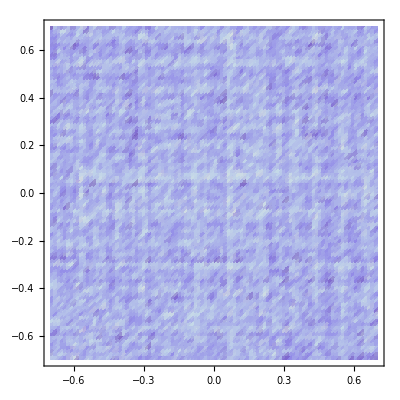

```mathematica
ListDensityPlot[norm,Mesh->False,DataRange->{{-10^6 limitn,10^6 limitn},{-10^6 limitm,10^6 limitm}}]
```

```mathematica
(*Export["int4.dat",norm]*)
```

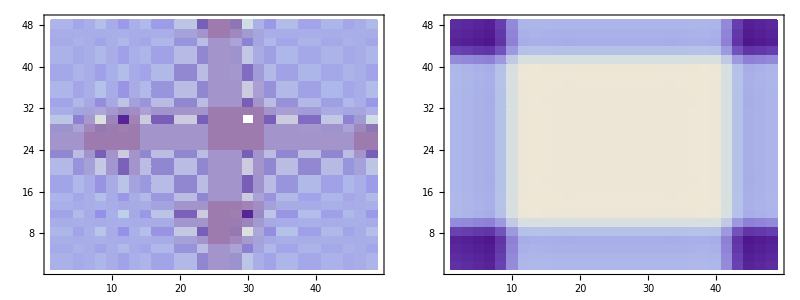

```mathematica
Block[{d=1000,n=48,tab,ftab},
tab=Table[Sinc[π x]Sinc[π y],{x,-d,d,2d/n},{y,-d,d,2d/n}];
ftab=Fourier[RotateLeft[tab,{n/2,n/2}]];
TableForm@{{ListDensityPlot[tab,Mesh->False,PerformanceGoal->"Speed"],ListDensityPlot[Re@ftab,Mesh->False,PerformanceGoal->"Speed"]}}
]
```